```mathematica
(* BinomialCoefficient *)
(* ({{n}, {m}})=(n!)/(m!(n-m)!)=({{n}, {n-m}}) *)
Binomial[4,2]
```

6

```mathematica
(* prob. of getting m H in n flips *)
(* ({{n}, {m}})(1/2)^m(1/2)^(n-m)=({{n}, {m}})(1/2)^n *)
N[Binomial[4,2]*(1/2)^4]
```

0.375

```mathematica
(* Arbitrary p:
 prob. of m success in n trials 
P(m)=({{n}, {m}})(p)^m(1-p)^(n-m)
Binomial Dist. *)
PDF[BinomialDistribution[n,p],m]
```

Piecewise[{{(1-p)^(-m+n) p^m Binomial[n,m], 0≤m≤n}, {0, True}}]

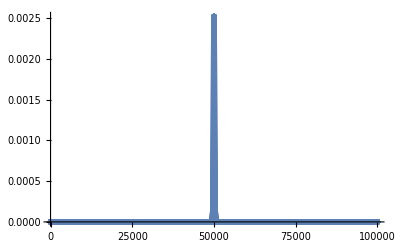

```mathematica
n=100000;p=0.5;
binomialdist=Table[{m,PDF[BinomialDistribution[n,p],m]},{m,0,n}];
ListPlot[binomialdist,PlotStyle->PointSize[0.01],PlotRange->All]
```

```mathematica
(* n->∞;pn remains large;Binomialdist. -> P(m)=1/(√(2π)σ)ⅇ^(-(m-np)^2/2 σ^2)
Normal/Gaussian dist. mean=np;std. dev.=σ=√(np(1-p)) *)
```

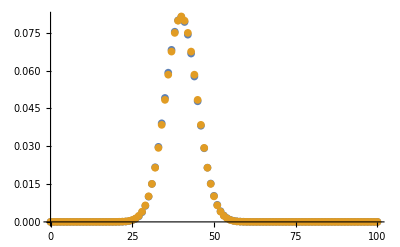

```mathematica
n=100;p=0.4;
binomialdist=Table[{m,PDF[BinomialDistribution[n,p],m]},{m,0,n}];
σ=√(n p(1-p));
g[m_]:=1/(√(2π) σ)ⅇ^(-(m-n p)^2/(2 σ^2));
gaussdist=Table[{m,g[m]},{m,0,n}];
ListPlot[{binomialdist,gaussdist},PlotRange->All]
```

```mathematica
(* Continuous Gaussian P(x)=1/(√(2π)σ)ⅇ^(-(x-<x>)^2/2 σ^2) *)
```

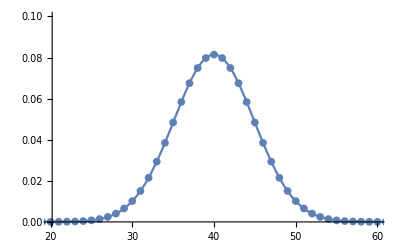

```mathematica
n=100;p=0.4;
σ=√(n p(1-p));
g[m_]:=1/(√(2π) σ)ⅇ^(-(m-n p)^2/(2 σ^2));
gaussdist=Table[{m,g[m]},{m,0,n}];
discrete=ListPlot[gaussdist,PlotRange->{{20,60},{0,0.10}}];
mean=40;
continuous=Plot[PDF[NormalDistribution[mean,σ],x],{x,20,60},PlotRange->{{20,60},{0,0.10}}];
Show[discrete,continuous]
```

```mathematica
Clear[n,p];
PDF[BinomialDistribution[n,p],m]
```

Piecewise[{{(1-p)^(-m+n) p^m Binomial[n,m], 0≤m≤n}, {0, True}}]

```mathematica
Mean[BinomialDistribution[n,p]]
```

n p

```mathematica
StandardDeviation[BinomialDistribution[n,p]]
```

√(n (1-p) p)

```mathematica
Clear[mean,sigma];PDF[NormalDistribution[mean,sigma],x]
```

(ⅇ^(-(-mean+x)^2/(2 sigma^2)))/(√(2 π) sigma)

```mathematica
Mean[NormalDistribution[mean,sigma]]
```

mean

```mathematica
StandardDeviation[NormalDistribution[mean,sigma]]
```

sigma

```mathematica
(* part. diff. in 1-D
P(x,t)=1/(√(2π)σ(t))ⅇ^(-x^2/2σ(t)^2),σ(t)=√(2Dt) *)
Clear[sigma,d,t,p];
d=1;sigma[t_]:=√(2 d t);
p[x_,t_]:=1/(√(2π)sigma[t])*ⅇ^(-x^2/(2 sigma[t]^2));
Animate[Plot[p[x,t],{x,-10,10},PlotRange->{0,0.3},PlotStyle->{Thick,Black},Filling->Axis,AxesLabel->{"x","P(,t)"}],{t,0.001,100,0.5},AnimationRepetitions->1]
```

```mathematica
ψ[x_,y_]:=2*Sin[nx*Pi*x]*Sin[ny*Pi*y];
nx=5;
ny=5;
Plot3D[ψ[x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-